# Synthetic Lethal partner inference

```mathematica
$Path = $Path ∪ {NotebookDirectory[]} ;Needs["Booned`"];Needs["ActONetLib`"];
```

```mathematica
controltype=ControlDefinition
```

ControlDefinition

```mathematica
boolcolor={False-> Darker[Red,0.4],True-> Darker[Green,0.6]};
SetAttributes[CoreForm,Listable]
CoreForm[act_-> val_]:= Style[  act,val/.boolcolor,10,FontFamily->"Helvetica"]
```

## Network Analysis DISEASE → DRUG

### ⋆ Boolean Network Definition

```mathematica
F= {EGFR->!BRCA1,ERK12-> EGFR,PIK3CA->!PTEN&&EGFR,Akt->PIK3CA,GSK3->!Akt, MDM2->Akt && p53,p53->!MDM2 && (BRCA1|| !PARP1),PTEN->p53,PARP1->ERK12,BRCA1->¬CycD1,Bcl2->Akt,Bax->!Bcl2&&p53,CycD1->(!GSK3&&ERK12)||(!BRCA1&&PARP1)};
```

```mathematica
Fact= {EGFR->!BRCA1,ERK12-> EGFR,PIK3CA->!PTEN&&EGFR,Akt->PIK3CA,GSK3->!Akt, MDM2->Akt && p53,p53->!MDM2 && (BRCA1|| !PARP1),PTEN->p53,PARP1->ERK12,BRCA1->False,Bcl2->Akt,Bax->!Bcl2&&p53,CycD1->(!GSK3&&ERK12)||(!BRCA1&&PARP1)};
```

#### Information on network

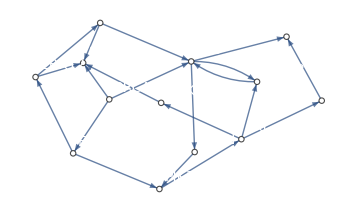
EGFR→¬BRCA1
ERK12→EGFR
PIK3CA→¬PTEN∧EGFR
Akt→PIK3CA
GSK3→¬Akt
MDM2→Akt∧p53
p53→¬MDM2∧(BRCA1∨¬PARP1)
PTEN→p53
PARP1→ERK12
BRCA1→False
Bcl2→Akt
Bax→¬Bcl2∧p53
CycD1→(¬GSK3∧ERK12)∨(¬BRCA1∧PARP1)-Graphics-  | 1
EGFR | -Graphics3D-
ERK12 | -Graphics3D-
PIK3CA | -Graphics3D-
Akt | -Graphics3D-
GSK3 | -Graphics3D-
MDM2 | -Graphics3D-
p53 | -Graphics3D-
PTEN | -Graphics3D-
PARP1 | -Graphics3D-
BRCA1 | -Graphics3D-
Bcl2 | -Graphics3D-
Bax | -Graphics3D-
CycD1 | -Graphics3D-
■ | ■

```mathematica
Row[{Panel@TraditionalForm@TableForm[Fact],ig=InteractionGraph[Fact,ImageSize->Medium],NiceStableStates[Fact]},Spacer[50]]
```

### Marking definition and satisfiability test

```mathematica
markers={CycD1,Bax}
```

{CycD1,Bax}

```mathematica
marking={CycD1->False,Bax->True}
```

{CycD1→False,Bax→True}

```mathematica
sys=StabilityCondition[Fact]/.marking; isat=SatisfiableQ[sys];
```

```mathematica
TableForm[{NiceStableStates[marking], Panel[Row[{Style["Satisfiable system","Helvetica",14],Checkbox[isat, Enabled->False]},"  "]]}, TableAlignments->Center]
```

| 1
CycD1 | -Graphics3D-
Bax | -Graphics3D-
■ | ■
    Satisfiable system

### List of variables that are allowed to be frozen either True or False

By definition  the markers cannot be frozen

```mathematica
frozenfalse=Complement[Agents[Fact],markers]
```

{Akt,Bcl2,BRCA1,EGFR,ERK12,GSK3,MDM2,p53,PARP1,PIK3CA,PTEN}

```mathematica
frozentrue=Complement[Agents[Fact],markers]
```

{Akt,Bcl2,BRCA1,EGFR,ERK12,GSK3,MDM2,p53,PARP1,PIK3CA,PTEN}

### Core

Computation of the core

```mathematica
Highlighted[TableForm[Timing[Column@CoreForm[cores=Destify[Fact,Nothing,MarkingToFormula[marking],frozenfalse,frozentrue,ControlType->controltype]]]],Frame-> True]
```

0.015625
{EGFR}
{PARP1}
{ERK12}
{BRCA1}

## Validation of the solutions

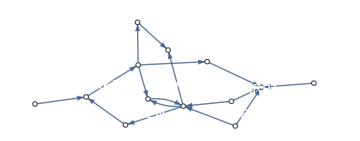
EGFR→False
ERK12→False
PIK3CA→!PTEN&&EGFR
Akt→PIK3CA
GSK3→!Akt
MDM2→Akt&&p53
p53→!MDM2&&(BRCA1||!PARP1)
PTEN→p53
PARP1→False
BRCA1→True
Bcl2→Akt
Bax→!Bcl2&&p53
CycD1→(!GSK3&&ERK12)||(!BRCA1&&PARP1)
-Graphics-  | 1
EGFR | -Graphics3D-
ERK12 | -Graphics3D-
PIK3CA | -Graphics3D-
Akt | -Graphics3D-
GSK3 | -Graphics3D-
MDM2 | -Graphics3D-
p53 | -Graphics3D-
PTEN | -Graphics3D-
PARP1 | -Graphics3D-
BRCA1 | -Graphics3D-
Bcl2 | -Graphics3D-
Bax | -Graphics3D-
CycD1 | -Graphics3D-
■ | ■{EGFR→False}
EGFR→False
ERK12→False
PIK3CA→!PTEN&&EGFR
Akt→PIK3CA
GSK3→!Akt
MDM2→Akt&&p53
p53→!MDM2&&(BRCA1||!PARP1)
PTEN→p53
PARP1→False
BRCA1→True
Bcl2→Akt
Bax→!Bcl2&&p53
CycD1→(!GSK3&&ERK12)||(!BRCA1&&PARP1)
-Graphics-  | 1
EGFR | -Graphics3D-
ERK12 | -Graphics3D-
PIK3CA | -Graphics3D-
Akt | -Graphics3D-
GSK3 | -Graphics3D-
MDM2 | -Graphics3D-
p53 | -Graphics3D-
PTEN | -Graphics3D-
PARP1 | -Graphics3D-
BRCA1 | -Graphics3D-
Bcl2 | -Graphics3D-
Bax | -Graphics3D-
CycD1 | -Graphics3D-
■ | ■{PARP1→False}
EGFR→False
ERK12→False
PIK3CA→!PTEN&&EGFR
Akt→PIK3CA
GSK3→!Akt
MDM2→Akt&&p53
p53→!MDM2&&(BRCA1||!PARP1)
PTEN→p53
PARP1→False
BRCA1→True
Bcl2→Akt
Bax→!Bcl2&&p53
CycD1→(!GSK3&&ERK12)||(!BRCA1&&PARP1)
-Graphics-  | 1
EGFR | -Graphics3D-
ERK12 | -Graphics3D-
PIK3CA | -Graphics3D-
Akt | -Graphics3D-
GSK3 | -Graphics3D-
MDM2 | -Graphics3D-
p53 | -Graphics3D-
PTEN | -Graphics3D-
PARP1 | -Graphics3D-
BRCA1 | -Graphics3D-
Bcl2 | -Graphics3D-
Bax | -Graphics3D-
CycD1 | -Graphics3D-
■ | ■{ERK12→False}
EGFR→False
ERK12→False
PIK3CA→!PTEN&&EGFR
Akt→PIK3CA
GSK3→!Akt
MDM2→Akt&&p53
p53→!MDM2&&(BRCA1||!PARP1)
PTEN→p53
PARP1→False
BRCA1→True
Bcl2→Akt
Bax→!Bcl2&&p53
CycD1→(!GSK3&&ERK12)||(!BRCA1&&PARP1)
-Graphics-  | 1
EGFR | -Graphics3D-
ERK12 | -Graphics3D-
PIK3CA | -Graphics3D-
Akt | -Graphics3D-
GSK3 | -Graphics3D-
MDM2 | -Graphics3D-
p53 | -Graphics3D-
PTEN | -Graphics3D-
PARP1 | -Graphics3D-
BRCA1 | -Graphics3D-
Bcl2 | -Graphics3D-
Bax | -Graphics3D-
CycD1 | -Graphics3D-
■ | ■{BRCA1→True}

```mathematica
TableForm[Function[sol, With[{Fres=ActNet[Fact,cores]},
Panel[Column[
{
Column[Fres],
Row[{InteractionGraph[Fres,ImageSize-> Medium],NiceStableStates[Fres]},Spacer[20]]
}],Style[sol, FontFamily->"Calibri Light",FontSize->14,FontColor -> White,Background->If[SatisfiableQ@StabilityCondition[Fres]/.marking,GrayLevel[0.4],Red]]
,
Alignment->{Top,Center}]
]]/@cores]
```